```mathematica
𝕩3={ψ,κ,φ};
(*Funktion des Gebietsüberlapps*)
f[ψ_,κ_]=κ + (√-eta2)/(√eta1)ψ - √-eta2;
sd=Table[D[f[κ,ψ],𝕩3[[i]]],{i,1,3}]
γc={{(a0^2 (8 κ^2+8 ψ^2))/(2 (Cos[2 κ ψ]-Cosh[κ^2-ψ^2])^2),0,0},{0,(a0^2 (8 κ^2+8 ψ^2))/(2 (Cos[2 κ ψ]-Cosh[κ^2-ψ^2])^2),0},{0,0,(a0^2 (1-Cos[4 κ ψ]))/(2 (Cos[2 κ ψ]-Cosh[κ^2-ψ^2])^2)}};
γcinv=Inverse[γc];
su=Table[Sum[γcinv[[i,j]]sd[[j]],{j,1,3}],{i,1,3}]
```

{1,(√-eta2)/(√eta1),0}

{(2 (Cos[2 κ ψ]-Cosh[κ^2-ψ^2])^2)/(a0^2 (8 κ^2+8 ψ^2)),(2 √-eta2 (Cos[2 κ ψ]-Cosh[κ^2-ψ^2])^2)/(a0^2 √eta1 (8 κ^2+8 ψ^2)),0}

```mathematica
𝕪3={ρ,z,φ};
ρ=-(a0 Sin[2 κ ψ])/(Cos[2 κ ψ]-Cosh[κ^2-ψ^2]);
z=+a0 Sinh[κ^2-ψ^2]/(Cos[2 κ ψ]-Cosh[κ^2-ψ^2]);
φ=φ;
T=Table[D[𝕪3[[i]],𝕩3[[j]]],{i,1,3},{j,1,3}];
s𝕪u=Simplify[Table[Sum[su[[i]]T[[j,i]],{i,1,3}],{j,1,3}]];
```

```mathematica
Solve[f[ψ,κ]==0,κ]
```

{{κ→(√-eta2 (√eta1-ψ))/(√eta1)}}

```mathematica
Simplify[s𝕪u/.κ->(√-eta2 (√eta1-ψ))/(√eta1)]
```

{-(√ArcSinh[1]-√ArcSinh[1] Cos[2 ψ (-ψ+√ArcSinh[1])] Cosh[2 ψ √ArcSinh[1]-ArcSinh[1]]+(-2 ψ+√ArcSinh[1]) Sin[2 ψ (ψ-√ArcSinh[1])] Sinh[2 ψ √ArcSinh[1]-ArcSinh[1]])/(2 (2 ψ^2-2 ψ √ArcSinh[1]+ArcSinh[1])),(4 ψ-2 √ArcSinh[1]+(-2 ψ+(1-ⅈ) √ArcSinh[1]) Cosh[((1+ⅈ) ψ-ⅈ √ArcSinh[1])^2]+(-2 ψ+(1+ⅈ) √ArcSinh[1]) Cosh[((-1-ⅈ) ψ+√ArcSinh[1])^2])/(4 (2 ψ^2-2 ψ √ArcSinh[1]+ArcSinh[1])),0}

```mathematica
Simplify[ρ/.κ->(√-eta2 (√eta1-ψ))/(√eta1)]
Simplify[z/.κ->(√-eta2 (√eta1-ψ))/(√eta1)]
```

Sin[2 ψ (ψ-√ArcSinh[1])]/(Cos[2 ψ (-ψ+√ArcSinh[1])]-Cosh[2 ψ √ArcSinh[1]-ArcSinh[1]])

-Sinh[2 ψ √ArcSinh[1]-ArcSinh[1]]/(Cos[2 ψ (-ψ+√ArcSinh[1])]-Cosh[2 ψ √ArcSinh[1]-ArcSinh[1]])

```mathematica
plot=Simplify[s𝕪u/.κ->(√-eta2 (√eta1-ψ))/(√eta1)]/.eta1->88/100/.eta2->-88/100/.a0->1
```

{((22 √22)/125-22/125 √22 Cos[2 ((√22)/5-ψ) ψ] Cosh[((√22)/5-ψ)^2-ψ^2]-(-(22 √22)/125+(44 ψ)/25) Sin[2 ((√22)/5-ψ) ψ] Sinh[((√22)/5-ψ)^2-ψ^2])/(2 ((44 √22 ψ)/125-(22 ψ^2)/25+22/25 (-22/25-ψ^2))),1/(2 ((44 √22 ψ)/125-(22 ψ^2)/25+22/25 (-22/25-ψ^2)))((-(22 √22)/125+(44 ψ)/25) Cos[2 ((√22)/5-ψ) ψ] Cosh[((√22)/5-ψ)^2-ψ^2]-(-(22 √22)/125+(44 ψ)/25) Cosh[((√22)/5-ψ)^2-ψ^2]^2-Sinh[((√22)/5-ψ)^2-ψ^2] (22/125 √22 Sin[2 ((√22)/5-ψ) ψ]-(-(22 √22)/125+(44 ψ)/25) Sinh[((√22)/5-ψ)^2-ψ^2])),0}

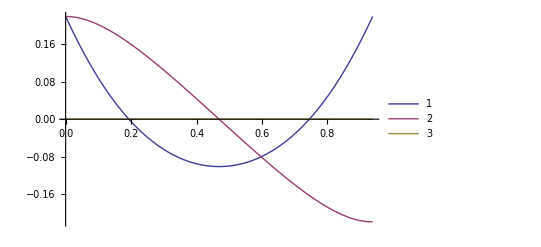

```mathematica
Plot[plot,{ψ,0,√(88/100)},PlotLegends->Automatic]
```

```mathematica
CForm[Simplify[s𝕪u/.κ->(√-eta2 (√eta1-ψ))/(√eta1)/.ψ->psi][[2]]]/.Power->pow/.Cosh->cosh/.Sinh->sinh/.Cos->cos/.Sin->sin
```

(pow(a0,-1)*pow(-2*eta2*psi*pow(eta1,0.5) + eta1*(eta2 - pow(psi,2)) + eta2*pow(psi,2),-1)*
     (cos(2*psi*pow(eta1,-0.5)*(-psi + pow(eta1,0.5))*pow(-eta2,0.5))*cosh(pow(psi,2) + eta2*pow(eta1,-1)*pow(-psi + pow(eta1,0.5),2))*
        (eta1*psi - eta2*psi + eta2*pow(eta1,0.5)) - (eta1*psi - eta2*psi + eta2*pow(eta1,0.5))*
        pow(cosh(pow(psi,2) + eta2*pow(eta1,-1)*pow(-psi + pow(eta1,0.5),2)),2) + 
       sinh(pow(psi,2) + eta2*pow(eta1,-1)*pow(-psi + pow(eta1,0.5),2))*
        (eta1*pow(-eta2,0.5)*sin(2*psi*pow(eta1,-0.5)*(-psi + pow(eta1,0.5))*pow(-eta2,0.5)) + 
          (eta1*psi - eta2*psi + eta2*pow(eta1,0.5))*sinh(pow(psi,2) + eta2*pow(eta1,-1)*pow(-psi + pow(eta1,0.5),2)))))/2.

5

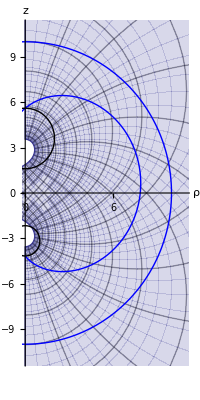

```mathematica
a0=3;
Rp=10;
r1=2;
r2=1;
eta1=ArcSinh[a0/r1];
eta2=-ArcSinh[a0/r2];
d1=Sqrt[a0^2+r1^2];
d2=-Sqrt[a0^2+r2^2];

ρρ=ρ/.κ->(√-eta2 (√eta1-ψ))/(√eta1);
zz=z/.κ->(√-eta2 (√eta1-ψ))/(√eta1);
plot0=ParametricPlot[{0,0},{ψ,0,π/2},PlotRange->{{0,Rp*1.1},{-Rp*1.1,Rp*1.1}},AxesLabel->{"ρ","z"}];
plot1=ParametricPlot[{ρ,z},{ψ,0,π/2},{κ,0,π/2},WorkingPrecision->100]//Quiet;
plot2=ParametricPlot[{{ρρ,zz},{Rp Cos[4ψ],Rp Sin[4ψ] }},{ψ,0,π/2}, PlotStyle->Blue]//Quiet;
plot3=ParametricPlot[{{r1 Cos[4ψ],r1 Sin[4ψ] + d1},{r2 Cos[4ψ],r2 Sin[4ψ] + d2}},{ψ,0,π/2}, PlotStyle->Black]//Quiet;
Show[plot0,plot1,plot2,plot3]
```